```mathematica
ConstraintViolations[array_]:=Count[Partition[array,{3,3},1],{{_,a_,_},{b_,x_,c_},{_,d_,_}}/;!(a+b+c+d==If[x==1,1,2]),{2}];
```

```mathematica
SeedRandom[3060];
arrs = NestList[With[{new=MapAt[1-#&,#,RandomInteger[{1,10},2]]},If[ConstraintViolations[new]>ConstraintViolations[#],#,new]]&,RandomChoice[{1,0},{10,10}],1000];
```

```mathematica
gas = GatherBy[arrs, ConstraintViolations];
```

```mathematica
gas2 = Gather[arrs];
```

```mathematica
subs =Subtract@@@Partition[gas[[All, 1]], 2, 1];
```

```mathematica
ps = SparseArray[#]["ExplicitPositions"]&/@ subs;
```

```mathematica
ps2 = SparseArray[#]["ExplicitPositions"]&/@ Subtract@@@Partition[gas2[[All, 1]], 2, 1];
```

```mathematica
allps = SparseArray[#]["ExplicitPositions"]&/@Subtract@@@Partition[arrs, 2, 1];
```

```mathematica
reps = MapThread[ReplacePart[#1, Thread[#2->Red]]&, {gas[[2;;,1]], ps}];
```

```mathematica
reps2 = MapThread[ReplacePart[#1, Thread[#2->Red]]&, {gas2[[2;;,1]], ps2}];
```

```mathematica
allreps = MapThread[ReplacePart[#1, Thread[#2->Red]]&, {arrs[[2;;]], allps}];
```

```mathematica
ListAnimate[ArrayPlot/@ reps]
```

```mathematica
ListAnimate[ArrayPlot/@ reps2]
```

```mathematica
ListAnimate[ArrayPlot/@ allreps[[;;10]]]
```

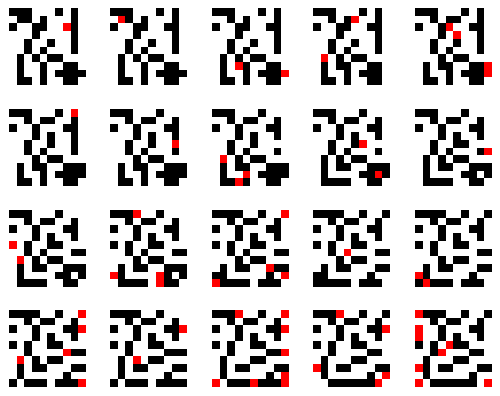

```mathematica
GraphicsGrid[Partition[ArrayPlot/@ reps, 5], ImageSize->{500, Automatic}]
```

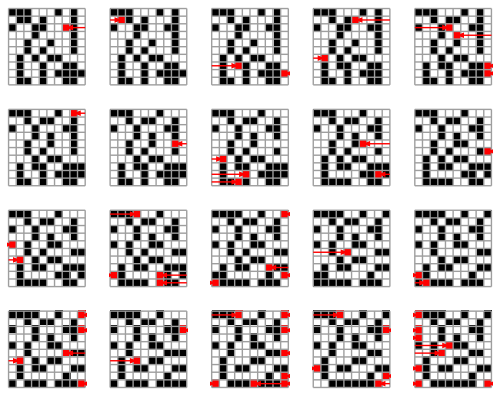

```mathematica
GraphicsGrid[Partition[MapThread[PerturbedArrayPlot[#1, #2]&,{reps,ps}], 5], ImageSize->{500, Automatic}]
```

```mathematica
ps2[[;;10]]
```

{{{3,8}},{{2,2}},{{9,10}},{{8,4}},{{7,2}},{{2,6}},{{8,10}},{{4,6}},{{9,10}},{{3,5}}}

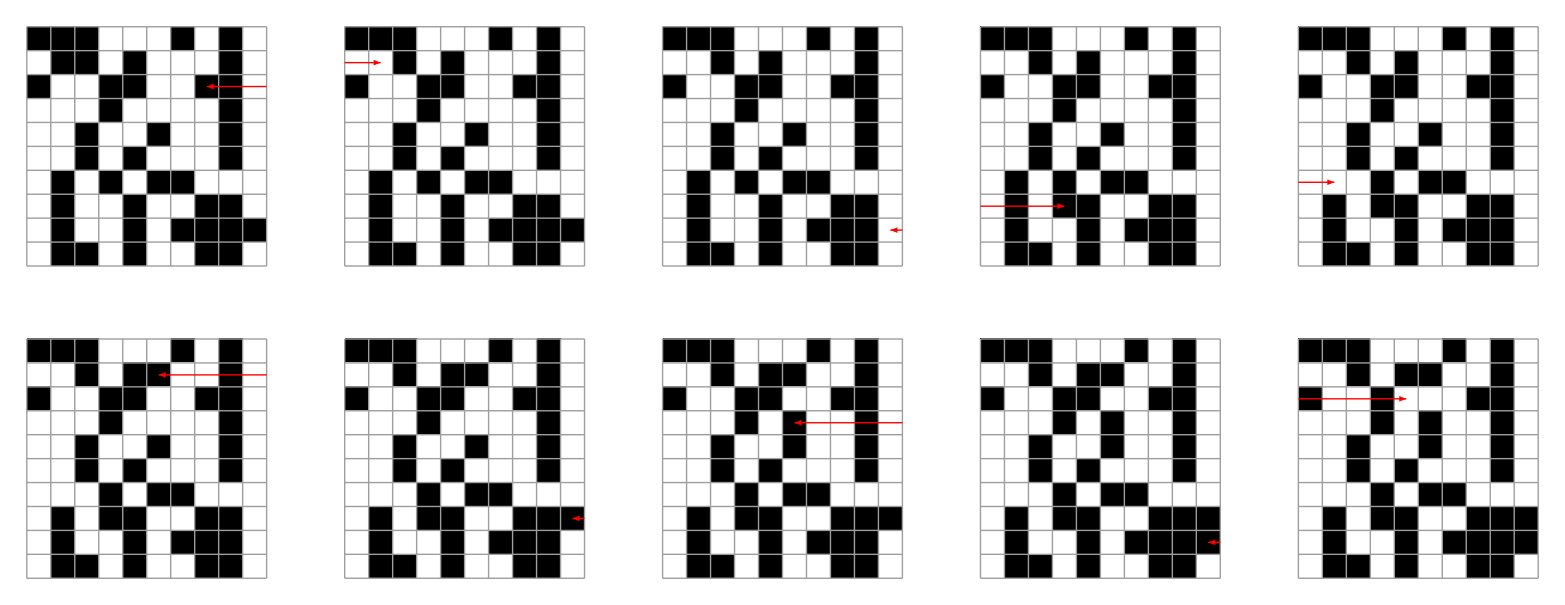

```mathematica
GraphicsGrid[Partition[MapThread[PerturbedArrayPlot[#1, #2, "ArrowStyle"->Arrowheads[.1]]&,{gas2[[2;;11, 1]],ps2[[;;10]]}], 5], ImageSize->{500, Automatic}]
```

```mathematica
ListAnimate[MapThread[PerturbedArrayPlot[#1, #2]&,{reps,ps}]]
```

### Anatomy

```mathematica
AnatomyPlot3D[{Entity["AnatomicalStructure","Aorta"],Entity["AnatomicalStructure","Heart"]}]
```

-Graphics3D-

```mathematica
AnatomyPlot3D[Entity["AnatomicalStructure","Heart"]]
```

-Graphics3D-

```mathematica
AnatomyPlot3D[Entity["AnatomicalStructure","Lung"]]
```

-Graphics3D-

```mathematica
AnatomyPlot3D[Entity["AnatomicalStructure","Kidney"]]
```

-Graphics3D-